```mathematica
UnitConvert[N@Quantity[12, "Volts"]/Quantity[30, "Kiloohms"],Quantity[, "Milliamperes"]]
```

0.4 mA

```mathematica
I1 = Quantity[12, "Volts"]/Quantity[10, "Kiloohms"];I2=Quantity[12, "Volts"]/Quantity[20, "Kiloohms"];N[totalCurrent=UnitConvert[I1+I2,Quantity[, "Milliamperes"]]]
```

1.8 mA

```mathematica
N@UnitConvert[Quantity[12, "Volts"]/totalCurrent,Quantity[, "Kiloohms"]]
N@UnitSimplify[1/(1/Quantity[10, "Kiloohms"]+1/Quantity[20, "Kiloohms"])]
```

6.66667 kΩ

6.66667 kΩ

## iSIM 2

```mathematica
With[{context="isim2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
ClearAll[t];
```

```mathematica
r=Quantity[10, "Kiloohms"];
c=Quantity[1, "Microfarads"];
```

```mathematica
eq1=vout[0]==1;
eq2=vout[t]==current[t]*r;
eq3=vout'[t]==current[t]*1/c;
```

```mathematica
ClearAll@current
```

```mathematica
DSolveValue[{eq1,eq2,eq3},{vout[t]},t]
```

Quantity::compat: 1/Microfarads and Kiloohms are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

$Aborted

```mathematica
D[E^(x/RC),x]
```

ⅇ^(x/RC)/RC

```mathematica
UnitSimplify[r*c]
```

1/100 s

```mathematica
With[{context="isim2`"},If[Context[]==context,End[],"Not in context"]]
```

isim2`

## isim3

```mathematica
With[{context="isim3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
var=((1+ⅈ) (3+ⅈ) (-2-ⅈ))/(ⅈ (3+4 ⅈ) (5+ⅈ));
```

```mathematica
Simplify@var
```

-11/65+(23 ⅈ)/65

```mathematica
N@%
```

-0.169231+0.353846 ⅈ

```mathematica
"convert to exponential"-0.16923076923076924+0.35384615384615387 ⅈWith[{n=Abs[-0.16923076923076924+0.35384615384615387 ⅈ],a=Arg[-0.16923076923076924+0.35384615384615387 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.392232 ⅇ^(ⅈ 2.0169)

```mathematica
With[{context="isim3`"},If[Context[]==context,End[],"Not in context"]]
```

isim3`

## iSim 4

```mathematica
With[{context="isim4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
z[t_]:=Exp[I t]-.3 Exp[I 3 t] + .2 Exp[I 5 t]
```

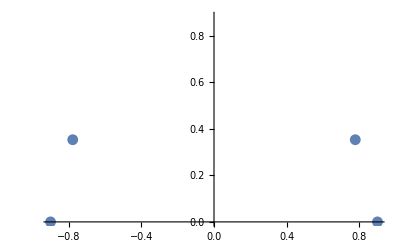

```mathematica
ListPlot[Table[{Re[z[t]],Im[z[t]]},{t,π {0,1/4,1/2,3/4,1}}],PlotTheme->"Minimal"]
```

```mathematica
Animate[ListPlot[{{Re@z[t],Im@z[t]}},PlotRange->2{{-1,1},{-1,1}}],{t,0,2*Pi}]
```

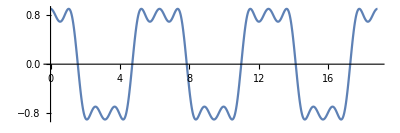

```mathematica
Plot[Re@z@t,{t,0,6 Pi},AspectRatio->1/3]
```

```mathematica
makePlot[t_]:=Module[{pt1,pt2},
Show[
ListPlot[{{Re@z[t],Im@z[t]}},PlotRange->2{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->{PointSize->.05,Red}],
Graphics[Circle[{0,0},1]],
pt1=Exp[I t];
Graphics[Circle[{Re@pt1,Im@pt1},.3]],
pt2 = pt1-.3Exp[3 I t];
Graphics[Circle[{Re@pt2,Im@pt2},.2]]
]
]
```

```mathematica
Animate[makePlot[t],{t,0,2 Pi}]
```

```mathematica
With[{context="isim4`"},If[Context[]==context,End[],"Not in context"]]
```

isim4`

## Difference Equations

```mathematica
With[{context="difference`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
eqn=x[n+1]==x[n]+3
```

x[1+n]==3+x[n]

```mathematica
RSolve[{eqn,x[0]==5},x[n],n]
```

{{x[n]→5+3 n}}

```mathematica
eqn2=x[n+1]==2x[n]+3
```

x[1+n]==3+2 x[n]

```mathematica
RSolve[{eqn2,x[0]==x0},x[n],n]
```

{{x[n]→-3+3 2^n+2^n x0}}

```mathematica
Fibonacci[100]
```

354224848179261915075

```mathematica
With[{context="difference`"},If[Context[]==context,End[],"Not in context"]]
```

difference`

## Template

```mathematica
With[{context="xxx"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="xxx"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

## Scratch work

```mathematica
eq=r c vc'[t]==vs[t]-vc[t]
```

c r vc'[t]==-vc[t]+vs[t]

```mathematica
Simplify@DSolveValue[{eq,vc[t]+vs[t]==1,vs[0]==5},{vc[t]},{t}][[1]]
```

1/2-9/2 ⅇ^(-(2 t)/(c r))

```mathematica
vc[t_]:=x1 Exp[x2 t]
```

```mathematica
eq
```

c ⅇ^(t x2) r x1 x2==-ⅇ^(t x2) x1+vs[t]